```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/sec_int_data/368nm.dat"]
```

{{1.63065,-0.938869},{1.58758,-0.916616},{1.51023,-0.862703},{1.46132,-0.832432},{1.41705,-0.786118},{1.38078,-0.761041},{1.34407,-0.73324},{1.30453,-0.716273},{1.27782,-0.689992},{1.24828,-0.673501},{1.22646,-0.673403},{1.20042,-0.657413},{1.183,-0.638545},{1.16401,-0.634312},{1.14739,-0.623752},{1.13423,-0.612028},{1.12389,-0.628484},{1.11401,-0.880393},{1.10574,-0.721999},{1.09905,-0.848726},{1.09389,-0.842042},{1.08918,-0.687344},{1.08895,-0.677038},{1.08874,-0.649264},{1.08738,-0.622018},{1.08767,-0.594606},{1.08994,-0.597473},{1.0948,-0.566462},{1.10288,-0.558949},{1.1168,-0.571921},{1.12832,-0.609339},{1.1517,-0.593664},{1.18117,-0.624797},{1.20042,-0.606731},{1.25083,-0.621552},{1.28067,-0.651123},{1.3108,-0.656102},{1.33715,-0.67356}}

-0.141822-0.448833 x

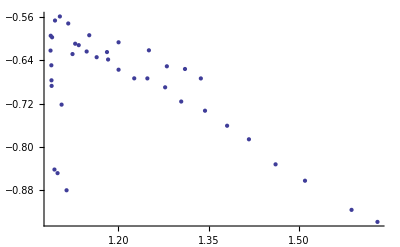

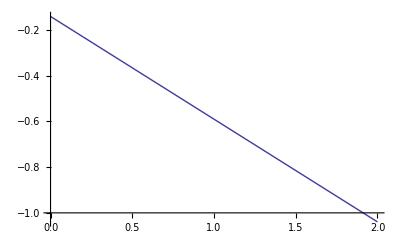

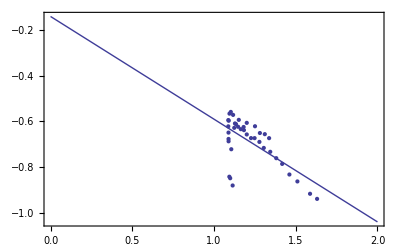

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```